```mathematica
NS[]
```

```mathematica
nn=1000;
```

```mathematica
prior[n_]=1/1001;
```

```mathematica
assu=(0<=n<=nn&&0<=d<=n&&0<=h<=nn-n)
```

0≤n≤1000&&0≤d≤n&&0≤h≤1000-n

```mathematica
ll[h_,d_,n_]=Assuming[assu,Simplify@PDF[HypergeometricDistribution[h+d,n,nn],d]]
```

(Binomial[1000-n,h] Binomial[n,d])/Binomial[1000,d+h]

```mathematica
ll[10,10,500]*100//N
```

17.7985

```mathematica
ll[10,10,5]*100//N
```

0.

```mathematica
upost[n_,h_,d_]=Assuming[assu,Simplify[prior[n]*ll[h,d,n]]]
```

(Binomial[1000-n,h] Binomial[n,d])/(1001 Binomial[1000,d+h])

```mathematica
zz[h_,d_]=Assuming[assu,Identity[Sum[upost[n,h,d],{n,0,nn}]]];
```

```mathematica
post[n_,h_,d_]=upost[n,h,d]/zz[h,d];
```

```mathematica
100*post[500,10,10]//N
```

0.373395

```mathematica
100*post[5,10,10]//N
```

0.

```mathematica
post[n,10,10]//N
```

6.1797×10^-44 Binomial[1000.-1. n,10.] Binomial[n,10.]

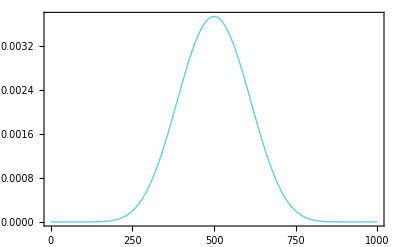

```mathematica
ListPlot[Table[post[n,10,10],{n,0,nn}],DataRange->{0,nn},Joined->True]
```

```mathematica
ll2[h_,d_,n_]=Boole[d<=n<=nn-h]
```

Boole[d≤n≤1000-h]

```mathematica
ll2[10,10,500]*100//N
```

100.

```mathematica
ll2[10,10,5]*100//N
```

0.

```mathematica
upost2[n_,h_,d_]=Simplify[prior[n]*ll2[h,d,n]]
```

Boole[d≤n≤1000-h]/1001

```mathematica
zz2[h_,d_]=Identity[Sum[upost2[n,h,d],{n,0,nn}]];
```

```mathematica
post2[n_,h_,d_]=upost2[n,h,d]/zz2[h,d];
```

```mathematica
100*post2[500,10,10]//N
```

0.101937

```mathematica
post2[5,10,10]
```

0

```mathematica
post2[n,10,10]//N
```

0.00101937 Boole[10.≤n≤990.]

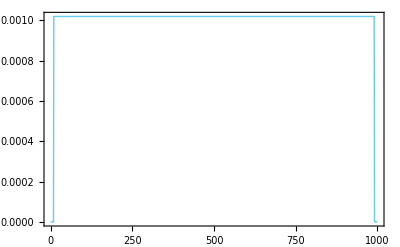

```mathematica
ListPlot[Table[post2[n,10,10],{n,0,nn}],DataRange->{0,nn},Joined->True]
```